### The script (1) computes the distance between the functions 2Sin[k π x] Sin[k π y] (k ∈ Integers) and their H^1-seminorm, and (2) demonstrates the lack of compactness of the L^2(0,1)-function class { Cos[k π x] : k ∈ Integers } using the Kolmogorov compactness theorem.

#### (1)

We define oscillatory functions on (0,1)^2.

```mathematica
ϕ[k_, x_,y_]:= 2Sin[k π x] Sin[k π y]
```

The plot shows the oscillatory behaviour of the functions

```mathematica
Manipulate[Plot3D[ϕ[k, x,y], {x, 0, 1}, {y, 0, 1}], {k, 1, 20}]
```

We compute the squared distance between phi_k and phi_j. The computation below assumes k \neq j.

```mathematica
Integrate[(ϕ[k, x,y]-ϕ[j, x,y])^2,{x, 0, 1}, {y, 0, 1}]
```

1/(4 j^2 k^2 (j^2-k^2)^2 π^2)(-32 j^2 k^4 Cos[k π]^2 Sin[j π]^2+k^2 (j^2-k^2)^2 Sin[2 j π]^2-32 j^4 k^2 Cos[j π]^2 Sin[k π]^2-4 j k^2 Sin[2 j π] ((j^2-k^2)^2 π-4 j^2 k Sin[2 k π])+(j^3-j k^2)^2 (8 k^2 π^2-4 k π Sin[2 k π]+Sin[2 k π]^2))

```mathematica
Simplify[%, {Element[k, Integers], Element[j,Integers]}]
```

2

We compute the H1-seminorm of phi_k.

```mathematica
D[ϕ[k, x,y], x]
```

2 k π Cos[k π x] Sin[k π y]

```mathematica
Integrate[(D[ϕ[k, x,y], x])^2,{x, 0, 1}, {y, 0, 1}] +Integrate[(D[ϕ[k, x,y], y])^2,{x, 0, 1}, {y, 0, 1}]
```

1/4 (-1+8 k^2 π^2+Cos[4 k π])

```mathematica
Simplify[%, Element[k, Integers]]
```

2 k^2 π^2

#### (2)

We investigate the lack of equicontinuity of the L^2(0,1)-function class { Cos[k π x] : k ∈ Integers }. The Kolmogorov compactness theorem then implies that this function class is noncompact.

```mathematica
ψ[k_, x_]:= Cos[k π x]
```

We define the zero-extension of ψ.

```mathematica
τ[k_, x_]:= Piecewise[{{0,x<0 || x > 1 },{ψ[k, x], 1>= x>=0}}]
```

```mathematica
Plot[f[10, x], {x, -2, 2}]
```

-Graphics-

Equicontinuity would require the following integral to converge towards zero as h -> 0 uniformly for all k.

```mathematica
Integrate[(τ[k, x+h]-ψ[k, x])^2,{x, 0, 1}, Assumptions->k ∈ Integers, Assumptions->h ∈ Interval[0,1]]
```

Piecewise[{{1/2, h>1||h≤-1}, {(2 h k π+Sin[2 h k π])/(4 k π), h==1}, {1/(4 k π)(2 h k π+8 k π Sin[(h k π)/2]^2-8 h k π Sin[(h k π)/2]^2+4 Sin[(-2+h) k π] Sin[(h k π)/2]^2+4 Sin[(h k π)/2]^2 Sin[h k π]+Sin[2 h k π]), 0<h<1}, {1/(4 k π)(-2 h k π+8 k π Sin[(h k π)/2]^2+8 h k π Sin[(h k π)/2]^2-4 Sin[(h k π)/2]^2 Sin[h k π]-Sin[2 h k π]-4 Sin[(h k π)/2]^2 Sin[(2+h) k π]), -1<h<0}, {0, True}}]

We choose h = 1/k and observe that the integral converges towards 2 as k approaches infinity.

```mathematica
Integrate[(τ[k, x+1/k]-ψ[k, x])^2,{x, 0, 1}, Assumptions->k ∈ Integers]
```

Piecewise[{{1/2, -1<k<0||0<k≤1}, {-1/(2 k), k==-1}, {(-3+4 k)/(2 k), k>1}, {(3+4 k)/(2 k), k<-1}, {0, True}}]

```mathematica
g[k_, h_]:=Integrate[(τ[k, x+h]-ψ[k, x])^2,{x, 0, 1}, Assumptions->k ∈ Integers, Assumptions->h ∈ Interval[0,1]]
```

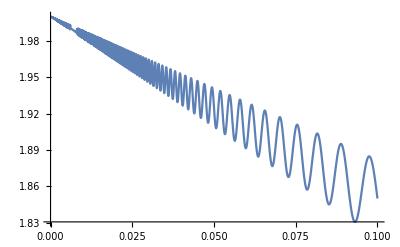

```mathematica
Plot[g[1/h, h], {h, 0, 1/10}]
```

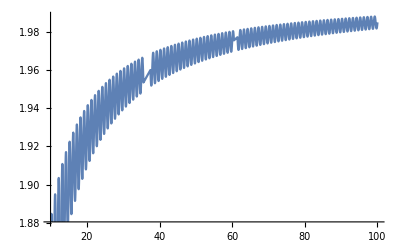

```mathematica
Plot[g[k, 1/k], {k, 10, 100}]
```